# Solving Nonlinear Equations

Chapter 1 uses the same equation in different scenarios:

```mathematica
f[x_] :=3x + Sin[x] -ⅇ^x;
f[x] //TraditionalForm
```

3 x-ⅇ^x+sin(x)

The derivative is also used:

```mathematica
f'[x]
```

3-ⅇ^x+Cos[x]

The plotted figure, as on p. 34:

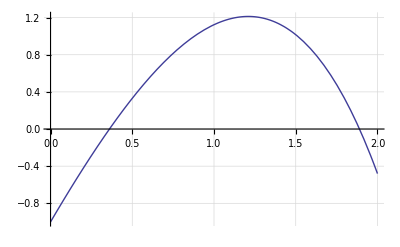

```mathematica
Plot[f[x], {x, 0, 2},
GridLines -> Automatic,
GridLinesStyle -> Dashed]
```